# GTR NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## Definitions and derivations

```mathematica
GTR`D[u_,α_,γ_]:=(α^(2 γ) (-1+α^2)  (-1+γ))/(π (-α^2+α^(2 γ)))1/((1+u^2 (-1+α^2))^γ)
```

```mathematica
GTR`D[u_,α_,1]:=(-1+α^2)/(2 π (1+u^2 (-1+α^2)) Log[α])
```

Similar to the Henyey Greenstein phase function:

```mathematica
FullSimplify[GTR`D[u,α,3/2],Assumptions->0<u<1&&0<α<1]
```

(α (1+α))/(2 π (1+u^2 (-1+α^2))^(3/2))

```mathematica
GTR`D[u_,α_,3/2]:=(α (1+α))/(2 π (1+u^2 (-1+α^2))^(3/2))
```

```mathematica
GTR`Λ[u_,α_,1]:=(-1+u √(1+(-1+1/u^2) α^2)+u Log[1+1/u]-u Log[1+√(1+(-1+1/u^2) α^2)])/(2 u Log[α])
```

```mathematica
GTR`σ[u_,α_,1]:=((-1+√(u^2+α^2-u^2 α^2)+u ArcSinh[u/(√(1-u^2))]+2 u Log[α]-u Log[(u+√(u^2+α^2-u^2 α^2))/(√(1-u^2))])/(2 Log[α]))
```

### height field normalization

```mathematica
Integrate[2Pi u GTR`D[u,α,γ],{u,0,1},Assumptions->0<α<1&&0<γ]
```

1

### distribution of slopes

```mathematica
FullSimplify[GTR`D[1/(√(p^2+q^2+1)),α,γ](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

((1+p^2+q^2)^(-2+γ) α^(2 γ) (-1+α^2) (p^2+q^2+α^2)^-γ (-1+γ))/(π (-α^2+α^(2 γ)))

```mathematica
FullSimplify[GTR`D[1/(√(p^2+q^2+1)),α,3/2](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

(α (1+α))/(2 π √(1+p^2+q^2) (p^2+q^2+α^2)^(3/2))

```mathematica
GTR`P22[p_,q_,α_,γ_]:=((1+p^2+q^2)^(-2+γ) α^(2 γ) (-1+α^2) (p^2+q^2+α^2)^-γ (-1+γ))/(π (-α^2+α^(2 γ)))
```

```mathematica
GTR`P22[p_,q_,α_,1]:=(-1+α^2)/(2 π (1+p^2+q^2) (p^2+q^2+α^2) Log[α])
```

```mathematica
GTR`P22[p_,q_,α_,3/2]:=(α (1+α))/(2 π √(1+p^2+q^2) (p^2+q^2+α^2)^(3/2))
```

Distribution of slope normalization test:

```mathematica
Integrate[GTR`P22[p,q,α,γ],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1&&γ>0]
```

1

Marginal slope distribution:

```mathematica
Integrate[GTR`P22[p,q,α,γ],{q,-Infinity,Infinity},Assumptions->α>0&&p>-7&&γ>1]
```

1/(2 √π (-α^2+α^(2 γ)))α^(2 γ) (-1+α^2) (-1+γ) (-((Gamma[-3/2+γ] (2 (p^2+α^2) (-2+γ) Hypergeometric2F1[-1/2,2-γ,5/2-γ,(1+p^2)/(p^2+α^2)]-(-1+α^2) (-3+2 γ) Hypergeometric2F1[1/2,2-γ,5/2-γ,(1+p^2)/(p^2+α^2)]))/((-1+α^2) (p^2+α^2)^(3/2) Gamma[γ]))+(2 (1+p^2)^(-3/2+γ) (p^2+α^2)^-γ Gamma[3/2-γ] Hypergeometric2F1[1/2,γ,-1/2+γ,(1+p^2)/(p^2+α^2)])/Gamma[2-γ])

```mathematica
GTR`P2[p_,α_,γ_]:=1/(2 √π (-α^2+α^(2 γ)))α^(2 γ) (-1+α^2) (-1+γ) (-((Gamma[-3/2+γ] (2 (p^2+α^2) (-2+γ) Hypergeometric2F1[-1/2,2-γ,5/2-γ,(1+p^2)/(p^2+α^2)]-(-1+α^2) (-3+2 γ) Hypergeometric2F1[1/2,2-γ,5/2-γ,(1+p^2)/(p^2+α^2)]))/((-1+α^2) (p^2+α^2)^(3/2) Gamma[γ]))+(2 (1+p^2)^(-3/2+γ) (p^2+α^2)^-γ Gamma[3/2-γ] Hypergeometric2F1[1/2,γ,-1/2+γ,(1+p^2)/(p^2+α^2)])/Gamma[2-γ])
```

```mathematica
Integrate[GTR`P22[p,q,α,1],{q,-Infinity,Infinity},Assumptions->α>0&&p>-7]
```

(1/(√(1+p^2))-1/(√(p^2+α^2)))/Log[α^2]

```mathematica
GTR`P2[q_,α_,1]:=(1/(√(1+q^2))-1/(√(q^2+α^2)))/Log[α^2]
```

```mathematica
Integrate[GTR`P22[p,q,α,3/2],{q,-Infinity,Infinity},Assumptions->α>0&&p>-7]
```

(α (-EllipticE[(-1+α^2)/(p^2+α^2)]+EllipticK[(-1+α^2)/(p^2+α^2)]))/(π (-1+α) √(p^2+α^2))

```mathematica
GTR`P2[q_,α_,3/2]:=(α (-EllipticE[(-1+α^2)/(p^2+α^2)]+EllipticK[(-1+α^2)/(p^2+α^2)]))/(π (-1+α) √(p^2+α^2))
```

### derivation of Λ(u)

```mathematica
FullSimplify[(√(1-u^2))/u Integrate[(q-u/(√(1-u^2)))GTR`P2[q,α,1],{q,u/(√(1-u^2)),Infinity},Assumptions->0<u<1&&0<α<1],Assumptions->0<u<1&&0<α<1]
```

(-1+u √(1+(-1+1/u^2) α^2)+u Log[1+1/u]-u Log[1+√(1+(-1+1/u^2) α^2)])/(2 u Log[α])

## Cross section σ(u) derivation

### sigma derivation

```mathematica
Integrate[(u-p √(1-u^2))GTR`P2[p,a,1],{p,-Infinity,u/(√(1-u^2))},Assumptions->0<u<1&&0<a<1]
```

(-1+√(a^2+u^2-a^2 u^2)+u ArcSinh[u/(√(1-u^2))]+2 u Log[a]-u Log[(u+√(a^2+u^2-a^2 u^2))/(√(1-u^2))])/(2 Log[a])

```mathematica
Delta`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

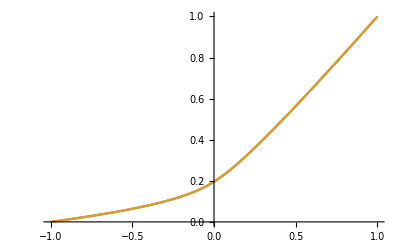

```mathematica
With[{α=.1},
Plot[{
Quiet[NIntegrate[GTR`D[ui,α,1]Delta`σ[u,ui],{ui,0,1}]],
((-1+√(u^2+α^2-u^2 α^2)+u ArcSinh[u/(√(1-u^2))]+2 u Log[α]-u Log[(u+√(u^2+α^2-u^2 α^2))/(√(1-u^2))])/(2 Log[α]))
},{u,-1,1}]
]
```